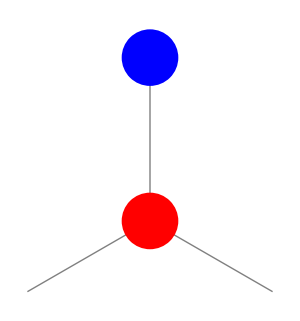

```mathematica
Clear["Global`*"]
unitCell[x_,y_]:={Gray,
,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Red,Disk[{x,y},0.1],Blue,Disk[{x,y+2/3 Sin[120 Degree]},0.1]};
Graphics[unitCell[0,0],ImageSize->300]
```

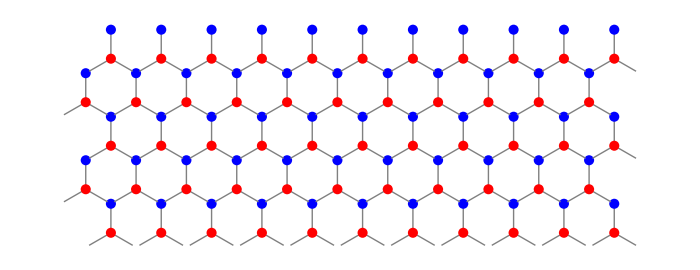

```mathematica
Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,1,5},{k,Ceiling[j/2],10+Ceiling[j/2]}]],ImageSize->700]
```

```mathematica
unitCell3D[x_,y_,z_]:={Red,Sphere[{x,y,z},0.1],Blue,Sphere[{x,y+2/3 Sin[120 Degree],z},0.1],Gray,Cylinder[{{x,y,z},{x,y+2/3 Sin[120 Degree],z}},0.05],Cylinder[{{x,y,z},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2,z}},0.05],Cylinder[{{x,y,z},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2,z}},0.05]}

Graphics3D[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree],0},unitVectB={1,0,0}},Table[unitCell3D@@(unitVectA j+unitVectB k),{j,20},{k,20}]],PlotRange->{{0,10},{0,10},{-1,1}}]
```

-Graphics3D-

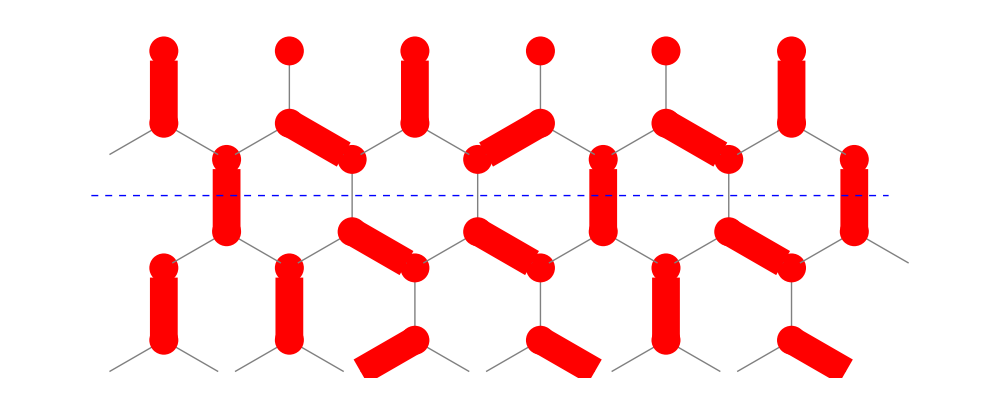

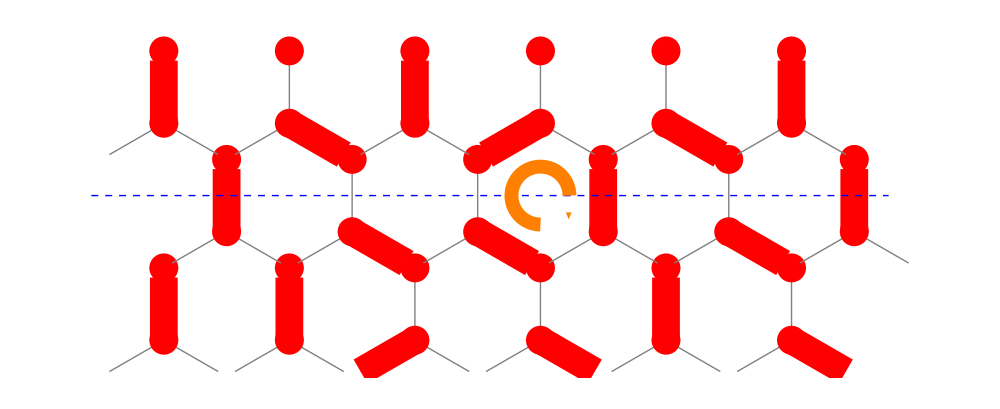

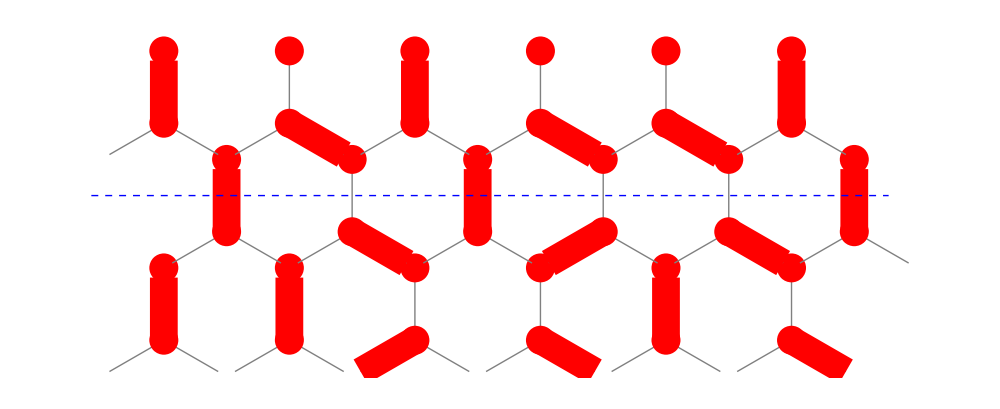

```mathematica
unitCell[x_,y_]:={Gray,
,Line[{{x,y},{x,y+Sqrt[3]*2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Sqrt[3]*Cos[30 Degree]/2,y-Sqrt[3]*Sin[30 Degree]/2}}],Line[{{x,y},{x-Sqrt[3]*Cos[30 Degree]/2,y-Sqrt[3]*Sin[30 Degree]/2}}],Red,Disk[{x,y},0.2],Red,Disk[{x,y+Sqrt[3]*2/3 Sin[120 Degree]},0.2]};

Bond1[vec_]:={Red,Thickness[0.02],Line[{{vec[[1]],vec[[2]]},{vec[[1]],vec[[2]]+Sqrt[3]*0.5}}]}
Bond2[vec_]:={Red,Thickness[0.02],Line[{{vec[[1]],vec[[2]]},{vec[[1]]-Sqrt[3]*Cos[30 Degree]/2,vec[[2]]-Sqrt[3]*Sin[30 Degree]/2}}]}
Bond3[vec_]:={Red,Thickness[0.02],Line[{{vec[[1]],vec[[2]]},{vec[[1]]+Sqrt[3]*Cos[30 Degree]/2,vec[[2]]-Sqrt[3]*Sin[30 Degree]/2}}]}


VecRight={Sqrt[3]*1,0};
VecUp={Sqrt[3]*Cos[120 Degree],Sqrt[3]*Sin[120 Degree]};

Cut[y_]:={Blue,Thick,Dashed,Line[{{-1,y},{10,y}}]};

BondSet={Bond1[{0,0}],Bond1[VecRight],Bond2[2VecRight],Bond3[3VecRight],Bond1[4VecRight],Bond3[5VecRight],Bond1[VecRight+VecUp],Bond3[2VecRight+VecUp],Bond3[3VecRight+VecUp],Bond1[4VecRight+VecUp],Bond3[5VecRight+VecUp],Bond1[6VecRight+VecUp],Bond1[1VecRight+2VecUp],Bond3[2VecRight+2VecUp],Bond1[3VecRight+2VecUp],Bond2[4VecRight+2VecUp],Bond3[5VecRight+2VecUp],Bond1[6VecRight+2VecUp]};

LatticeSet={Block[{unitVectA={Sqrt[3]*Cos[120 Degree],Sqrt[3]*Sin[120 Degree]},unitVectB={Sqrt[3]*1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,0,2},{k,Ceiling[j/2],5+Ceiling[j/2]}]]};

Tunnel[vec_]:={Orange,Thickness[0.01],Circle[{vec[[1]],vec[[2]]},0.4,{0 Degree,270 Degree}],Thickness[0],Arrow[{{vec[[1]]+0.4-0.01,vec[[2]]-0.33},{vec[[1]]+0.4-0.01,vec[[2]]-0.33-0.0001}}]};
 
CutSet1={Cut[Sqrt[3]*Sin[120 Degree]+Sqrt[3]/3 Sin[120 Degree]]};

CutSet2={Cut[Sqrt[3]*Sin[120 Degree]+Sqrt[3]/3 Sin[120 Degree]],Tunnel[3VecRight+{0,Sqrt[3]*Sin[120 Degree]+Sqrt[3]/3 Sin[120 Degree]}]};


Graphics[Join[LatticeSet,BondSet,CutSet1],ImageSize->1000]

Graphics[Join[LatticeSet,BondSet,CutSet2],ImageSize->1000]

BondSet2={Bond1[{0,0}],Bond1[VecRight],Bond2[2VecRight],Bond3[3VecRight],Bond1[4VecRight],Bond3[5VecRight],Bond1[VecRight+VecUp],Bond3[2VecRight+VecUp],Bond1[3VecRight+VecUp],Bond2[4VecRight+VecUp],Bond3[5VecRight+VecUp],Bond1[6VecRight+VecUp],Bond1[1VecRight+2VecUp],Bond3[2VecRight+2VecUp],Bond1[3VecRight+2VecUp],Bond3[4VecRight+2VecUp],Bond3[5VecRight+2VecUp],Bond1[6VecRight+2VecUp]};

Graphics[Join[LatticeSet,BondSet2,CutSet1],ImageSize->1000]
```

```mathematica
Sqrt[3]*2/3 Sin[120 Degree]
-Sqrt[3]*Cos[30 Degree]/2
```

1

-3/4